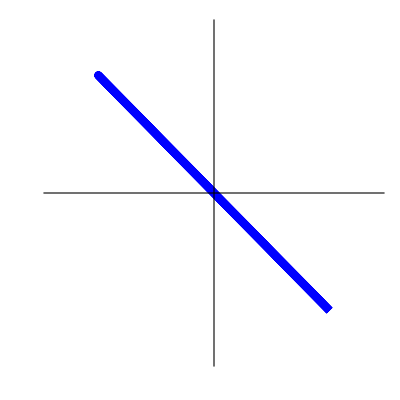

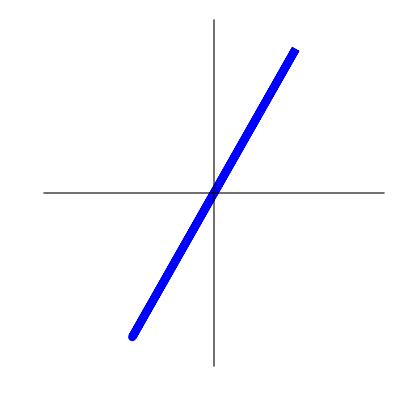

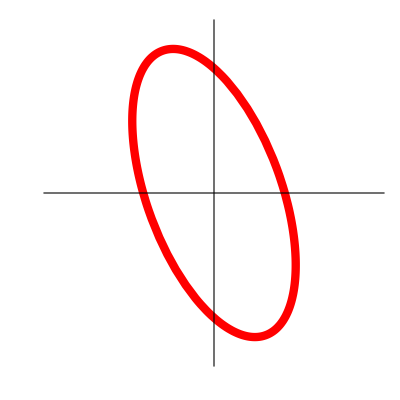

```mathematica
rad=1;
diagPol= ParametricPlot[{rad Cos[π/4] Cos[t], rad Sin[-π/4] Cos[t]}, {t, 0,2 π}, Axes->True, PlotStyle->{Blue, Arrowheads[{0.2,0.2}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}, Ticks->None, AxesStyle->Directive[Black, Thickness[0.005]]]/.Line->Arrow
interMedLinearPol= ParametricPlot[{rad Cos[π/3] Cos[t], rad Sin[π/3] Cos[t]}, {t, 0,2 π}, Axes->True, PlotStyle->{Blue, Arrowheads[{0.2,0.2}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}, Ticks->None, AxesStyle->Directive[Black, Thickness[0.005]]]/.Line->Arrow
ellipticalPol =  ParametricPlot[{rad Cos[π/3] Cos[t], rad Sin[π/3] Cos[t-(2π)/3]}, {t, 0,2 π}, Axes->True, PlotStyle->{Red, Arrowheads[{ 0, 0, 0.2, 0, 0, 0.2, 0}], Thickness[0.015]}, PlotRange->{{-1,1},{-1,1}}, Ticks->None, AxesStyle->Directive[Black, Thickness[0.005]]]/.Line->Arrow
SetDirectory[NotebookDirectory[]];
Export["diag_pol.svg", diagPol];
Export["intermediate_linear.svg", interMedLinearPol];
Export["elliptical_pol.svg", ellipticalPol];
```

```mathematica
χ = π/3;
ϕ = (2π)/3;
outJones = {{}{}}
```

{{}}